```mathematica
(* Reading in the data. *)
data = Import["C:/Users/ks121/Documents/Phys_567/04_Kevin_Shuman/Hist_Data.dat"];
data1 = Import["C:/Users/ks121/Documents/Phys_567/04_Kevin_Shuman/Hist_Data_00_1.dat"];
data2 = Import["C:/Users/ks121/Documents/Phys_567/04_Kevin_Shuman/Hist_Data_00_1_long.dat"];
```

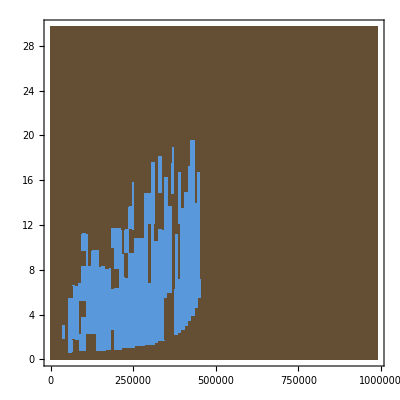
-Graphics-E_0 [V m^-1]ω [s^-1]

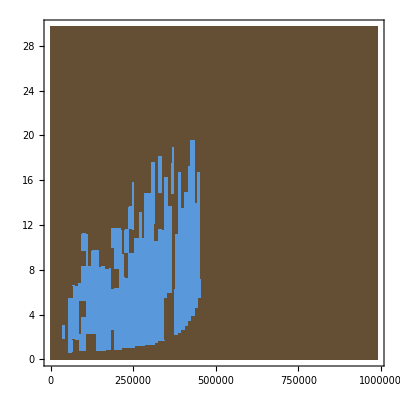
-Graphics-E_0 [V m^-1]ω [s^-1]

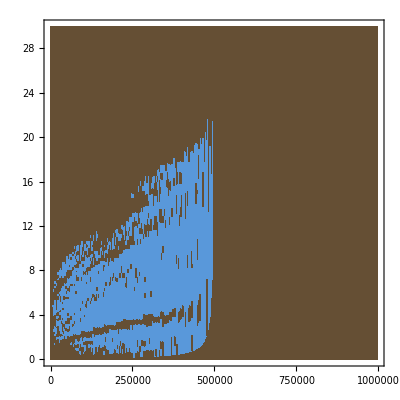
-Graphics-E_0 [V m^-1]ω [s^-1]

```mathematica
(* I and creating three histograms, the first with the data for a tolerance of 1 and 10,000 points, the second with a tolerance to 0.01 with 10,000 points, and the last with a tolerance of 0.1 with 250,000 points. *)
Labeled[ListDensityPlot[data,ColorFunction->"SouthwestColors", InterpolationOrder->0], {"E_0 [V m^-1]", "ω [s^-1]"}, {Bottom, Left}, RotateLabel->True]
Labeled[ListDensityPlot[data1,ColorFunction->"SouthwestColors", InterpolationOrder->0], {"E_0 [V m^-1]", "ω [s^-1]"}, {Bottom, Left}, RotateLabel->True]
Labeled[ListDensityPlot[data2,ColorFunction->"SouthwestColors", InterpolationOrder->0], {"E_0 [V m^-1]", "ω [s^-1]"}, {Bottom, Left}, RotateLabel->True]
```